### Soliton

```mathematica
t=0;
ClearAll[A]
ρ = 1.06;
E0 = 3.7;
nu = 0.34;
l = -18.9;
m = -13.3;
n = -10;
β=3 E0 + 2 l (1-2 nu)^3 + 4 m (1+nu)^2 (1 - 2 nu) + 6 n nu^2;
c = Sqrt[E0/ρ];
R = 5;
```

```mathematica
B[A_,a_,b_,d_]=Sqrt[(3A β c^2 ρ)/(-4 R^2 (a (A β+3 c^2 ρ)^2+3 c^2 ρ (A b β+3 c^2 (b+d) ρ)))];
V=Sqrt[(A β+3 c^2 ρ)/(3ρ)];
```

```mathematica
u1[A_] =  A Cosh [B[A,(1+nu)/4,(-1-nu-nu^2)/2,(1+nu)/4] (x - V t)]^(-2);
u12[A_]=A Cosh [B[A, (5-5nu-6 nu^2+4 nu^3)/(8(1-nu)),(-7+7nu+2 nu^2)/(8(1-nu)),1/4](x - V t)]^(-2);
u2[A_] =  A Cosh [B[A,0,(1-nu)nu/2,-nu/2] (x - V t)]^(-2);
u3[A_] =  A Cosh [B[A,0,-nu^2/2,0] (x - V t)]^(-2);
```

```mathematica
B[-0.07, (5-5nu-6 nu^2+4 nu^3)/(8(1-nu)),(-7+7nu+2 nu^2)/(8(1-nu)),1/4]
```

0.636165

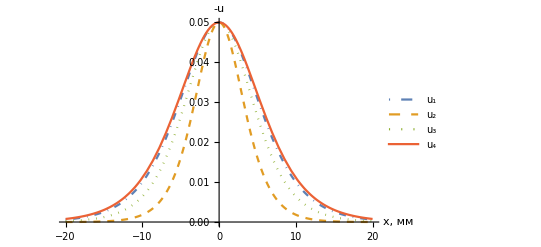

```mathematica
Amp=-0.05;
fig=Plot[{-u1[Amp], -u12[Amp],-u2[Amp], -u3[Amp]}, {x, -20, 20}, 
PlotLegends->LineLegend[{Subscript[u, 1],Subscript[u, 2],Subscript[u, 3],Subscript[u, 4]},LabelStyle->Directive[Black,16]],
PlotStyle->{{DotDashed(*, Black*)},{Dashed(*, Black*)},
{Dotted(*, Black*)}, {Solid(*,Black*)}},
AxesLabel->{"x, мм",-u},PlotRange->Full,
BaseStyle->{FontSize->14}
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["FourSolitonsColor.pdf",fig]
```

FourSolitonsColor.pdf

```mathematica
sbst1={a->(1+nu)/4,b->-(1+nu+nu^2)/2,d->(1+nu)/4};
sbst2={a-> (5-5nu-6 nu^2+4 nu^3)/(8(1-nu)),b->(-7+7nu+2 nu^2)/(8(1-nu)),d->1/4};
length[A_]=a (A β+3 c^2 ρ)^2+3 c^2 ρ (A b β+3 c^2 (b+d) ρ);
Plot[{length[A]/.sbst1,length[A]/.sbst2},{A,-0.2,0},PlotLegends->{"Our","Bostrom's"}]
```

-Graphics-

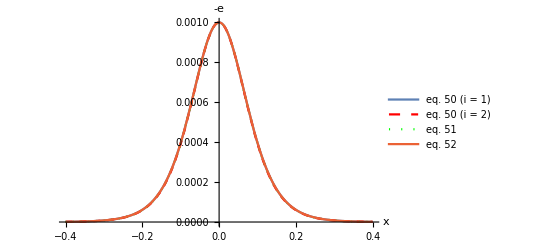

```mathematica
Amp=-0.001;
Plot[{-u1[Amp], -u12[Amp],-u2[Amp], -u3[Amp]}, {x, -0.4, 0.4}, 
AxesLabel->{x, -e},
PlotStyle->{Solid,{Dashed, Red},{Dotted, Green}}, PlotLegends->{"eq. 50 (i = 1)", "eq. 50 (i = 2)", "eq. 51", "eq. 52"}]
```

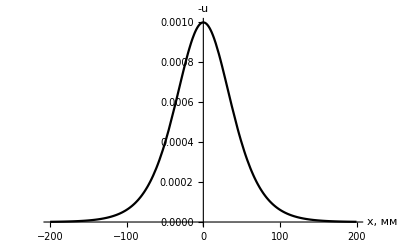

```mathematica
Amp=-0.001;
fig2=Plot[{-u1[Amp]}, {x, -200, 200}, PlotStyle->Black,
AxesLabel->{"x, мм", -u},BaseStyle->{FontSize->14}
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["SingleSoliton.pdf",fig2]
```

SingleSoliton.pdf

### Dispersive curves

```mathematica
(* Our equation *)

DD1 =( 4/(nu+1) +  (2 (nu^2 + nu + 1))/(nu+1) k^2)^2 - 4 (4/(nu+1) + k^2) k^2;
Omega3a[k_] = Sqrt[2/(nu+1) + (nu^2 + nu + 1)/(nu+1) k^2 - Sqrt[DD1/4]];
Omega3b[k_]= Sqrt[2/(nu+1) + (nu^2 + nu + 1)/(nu+1) k^2 + Sqrt[DD1/4]];

(* Boestrom *)
rho=ρ;
lambda = E0 nu/ ((1+nu) (1 - 2 nu));
mu = E0/(2 (1+nu));
α1 = ((lambda^2 + 5 lambda mu + 5 mu^2) (3 lambda + 2 mu))/(2 (lambda+mu)^2 (lambda + 2 mu));
α2 = (6 lambda^2 + 21 lambda mu + 14 mu^2)/(2 (lambda+mu) (lambda + 2 mu));
DD2= (4  + α2 k^2)^2 - 4 α1 (4 + k^2) k^2;
Omega4a[k_] = Sqrt[(4 + α2 k^2 - Sqrt[DD2])/(2α1)];
Omega4b[k_] = Sqrt[(4 + α2 k^2 + Sqrt[DD2])/(2α1)];
```

```mathematica
(* DDE *)
Omega2[k_] = Sqrt[((1-(nu/2)  k^2) k^2)/(1 + (nu-1)(nu/2) k^2)];
(* Ostrovsky-Sutin *)
Omega1[k_] =Sqrt[k^2/(1 + (nu^2/2) k^2)];
```

```mathematica
kR=k R;
```

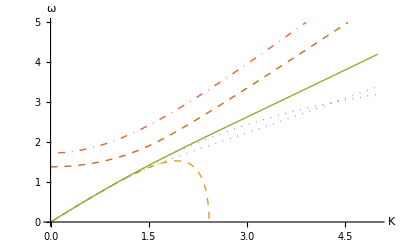

```mathematica
Plot[{Omega1[k],Omega2[k], Omega3a[k], Omega3b[k], 
Omega4a[k], Omega4b[k]}, {k, 0, 5}, AxesLabel->{K, ω},
PlotStyle->{{Dotted, Thick(*, Black*)},
{Dashed, Thick(*, Red*)},
{Solid, Thick(*, Blue*)},
{DotDashed, Thick(*, Purple*)}},
PlotRange->{0,5}]
```

```mathematica
rho=ρ;
lambda = E0 nu/ ((1+nu) (1 - 2 nu))
mu = E0/(2 (1+nu))
```

2.93377

1.3806

```mathematica
(* Pochhammer - Chree, from Boestrom, scaled omega-> omega R/ c and k-> k/R *)
ks = c ω/ R  Sqrt[rho/mu]

kp =  c ω /R  Sqrt[rho/(lambda + 2 mu)]

qs = Sqrt[ks^2 - k^2/ R^2]

qp = Sqrt[kp^2 - k^2 / R^2]
```

0.327414 ω

0.161208 ω

√(-k^2/25+0.1072 ω^2)

√(-k^2/25+0.0259879 ω^2)

```mathematica
Disp = ((ks^2 - 2 kp^2) BesselJ[0, qp R] + 2 qp^2  (D[BesselJ[1, x], x]/. x-> qp R)) (ks^2 - 2 k^2/ R^2) BesselJ[1, qs R] + 4 k^2/ R^2 qp qs BesselJ[1, qp R]  (D[BesselJ[1, x], x]/. x-> qs R) //Simplify
```

-0.08 (k^2-1.34 ω^2) BesselJ[1,5 √(-0.04 k^2+0.1072 ω^2)] ((-0.04 k^2+0.0812121 ω^2) BesselJ[0,5 √(-0.04 k^2+0.0259879 ω^2)]+(0.04 k^2-0.0259879 ω^2) BesselJ[2,5 √(-0.04 k^2+0.0259879 ω^2)])+2/25 k^2 √(-0.04 k^2+0.0259879 ω^2) √(-0.04 k^2+0.1072 ω^2) BesselJ[1,5 √(-0.04 k^2+0.0259879 ω^2)] (BesselJ[0,5 √(-0.04 k^2+0.1072 ω^2)]-BesselJ[2,5 √(-0.04 k^2+0.1072 ω^2)])

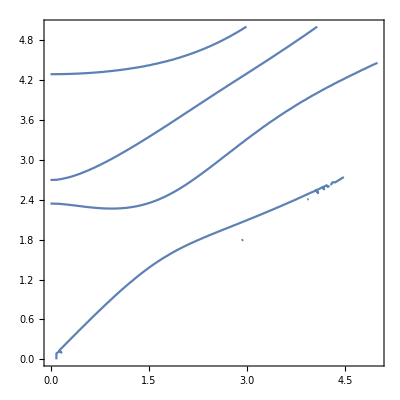

```mathematica
ContourPlot[{Disp==0}, {k, 0, 5}, {ω, 0, 5}]
```

```mathematica
ContourPlot[{Disp==0},{k,0,5},{ω,0,5},PerformanceGoal->"Quality"]
```

-Graphics-

```mathematica
ContourPlot[{Disp==0},{k,0,3},{ω,0,5},PerformanceGoal->"Quality",PlotPoints->1000,MaxRecursion->2]
```

$Aborted

```mathematica
(* As contour plots *)
G1 = ω^2 - k^2/(1 + (nu^2/2) k^2)

G2 =ω^2  - ((1-nu/2 k^2) k^2)/(1 + (nu (nu-1))/2 k^2)

G3 = ω^4 - ( 4/(nu+1) +  (2 (nu^2 + nu + 1))/(nu+1) k^2) ω^2  + (4/(nu+1) + k^2) k^2

G4 = α1 ω^4  - (4 + α2 k^2) ω^2 + (4 + k^2) k^2
```

-k^2/(1+0.0578 k^2)+ω^2

-(k^2 (1-0.17 k^2))/(1-0.1122 k^2)+ω^2

k^2 (2.98507+k^2)-(2.98507+2.17254 k^2) ω^2+ω^4

k^2 (4+k^2)-(4+3.32485 k^2) ω^2+2.09365 ω^4

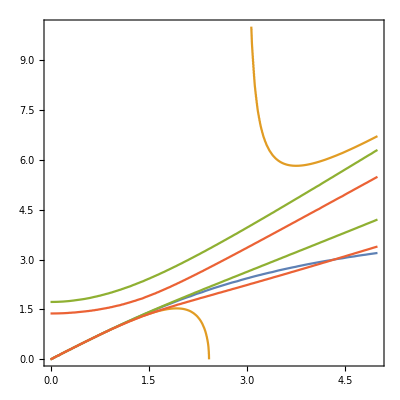

```mathematica
ContourPlot[{G1==0,G2 == 0, G3==0, G4==0}, {k, 0, 5}, {ω, 0, 10}]
```

```mathematica
(* Pochhammer - Chree, from Dai and Fan, scaled omega-> omega R/ C and k-> k/R *)
p = First[Sqrt[(rho c^2 ω^2)/((lambda + 2 mu) R^2) - k^2/R^2]]

q = First[Sqrt[(rho c^2 ω^2)/(mu R^2) - k^2/R^2]]
```

-10000 k^2+6496.97 ω^2

-10000 k^2+26800. ω^2

```mathematica
Dispexact=First[2 p / R (q^2 + k^2/ R^2 ) BesselJ[1, p R] BesselJ[1, q R] - (q^2 - k^2/ R^2 )^2 BesselJ[0, p R] BesselJ[1, q R] - 4 k^2/R^2 p q BesselJ[1,p R] BesselJ[0, q R]]
```

-40000 k^2 (-10000 k^2+6496.97 ω^2) (-10000 k^2+26800. ω^2) BesselJ[0,1/100 (-10000 k^2+26800. ω^2)] BesselJ[1,1/100 (-10000 k^2+6496.97 ω^2)]

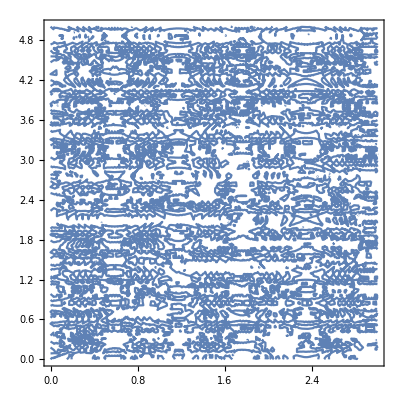

```mathematica
ContourPlot[Dispexact== 0, {k, 0, 3}, {ω,0, 5}]
```

```mathematica
Needs["PacletManager`"]
PacletInstall["~/Documents/MaTeX-1.7.5.paclet"]
```

Paclet[MaTeX,1.7.5,<>]

```mathematica
<<MaTeX`
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

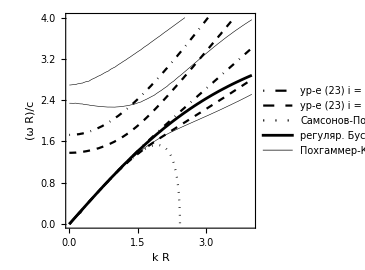

```mathematica
cp=ContourPlot[{G3==0, G4==0,G2==0,G1 == 0,Disp==0}, {k, 0, 4}, {ω, 0, 4}, (*GridLines->Automatic,*)
ContourStyle->{{ DotDashed,Black},{Dashed, Black},
{Dotted, Black},{AbsoluteThickness[2], Black},
{AbsoluteThickness[0.4], Black}},
PlotLegends->LineLegend[{
"ур-е (23) i = 1","ур-е (23) i = 2",
"Самсонов-Порубов",
"регуляр. Буссинеск",
"Похгаммер-Кри"},LabelStyle->Directive[Black,15]]];
figDisp=Show[cp,Axes->True,Frame->True,
FrameLabel->{"k R", Style["(ω R)/c",ScriptLevel->0]},
RotateLabel->False,
BaseStyle->{FontSize->14},ImageSize-> 270]
```

```mathematica
(* Legend: Disp - Pochhamme-Chree, G1 - Ostrovsky-Sutin (Love), G2 - DDE (Bishop...), G3 - our equation, G4 - Bostroem *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["2_DispBlackSmall.pdf",figDisp]
```

2_DispBlackSmall.pdf

```mathematica
(* Phase vesocities *)
V1 = v^2 k - k/(1 + (nu^2/2) k^2);
V2 =v^2k  - ((1-nu/2 k^2) k)/(1 + (nu (nu-1))/2 k^2);
V3 = v^4k^3 - ( 4/(nu+1) +  (2 (nu^2 + nu + 1))/(nu+1) k^2) v^2k  + (4/(nu+1) + k^2) k;

V4 = α1 v^4 k^3  - (4 + α2 k^2) v^2 k + (4 + k^2) k;
```

```mathematica
(* Pochhammer - Chree, from Boestrom, scaled omega-> omega R/ c and k-> k/R *)
k2s = c v/ R  Sqrt[rho/mu]k;

k2p =  c v /R  Sqrt[rho/(lambda + 2 mu)]k;

q2s = Sqrt[k2s^2 - k^2/ R^2];

q2p = Sqrt[k2p^2 - k^2 / R^2];
```

```mathematica
DispV = ((k2s^2 - 2 k2p^2) BesselJ[0, q2p R] + 2 q2p^2  (D[BesselJ[1, x], x]/. x-> q2p R))(k2s^2 - 2 k^2/ R^2) BesselJ[1, q2s R]+ 4 k^2/ R^2 q2p q2s BesselJ[1, q2p R]  (D[BesselJ[1, x], x]/. x-> q2s R)//Simplify;
```

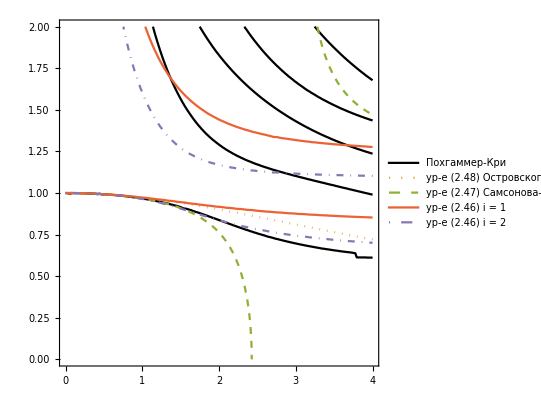

```mathematica
cp=ContourPlot[{DispV==0, V1==0,V2== 0, V3==0, V4==0}, {k, 0, 4}, {v, 0, 2}, 
ContourStyle->{{Solid, Thin, Black}, 
{Dotted, Thick(*, Black*)},{Dashed, Thick(*, Red*)},
{Solid, Thick(*, Blue*)},{DotDashed, Thick(*, Purple*)}},
PlotLegends->LineLegend[{"Похгаммер-Кри",
"ур-е (2.48) Островского-Сутина",
"ур-е (2.47) Самсонова-Порубова","ур-е (2.46) i = 1","ур-е (2.46) i = 2"},LabelStyle->Directive[Black,15]]]
```

```mathematica
ClearAll[k]
```

```mathematica
Φ[y_]=y BesselJ[0,y]/BesselJ[1,y];
C0=Sqrt[E0/ρ];
a=(v)^2(1+nu);
b=(1-2nu)(1-nu);
h1=k Sqrt[b a-1];
h2=k Sqrt[2 a-1];
```

```mathematica
Disp2=(a-1)^2 Φ[h1]-(b a-1)(a-Φ[h2]);
```

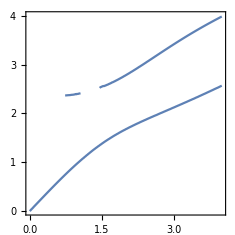

```mathematica
ContourPlot[{Disp2==0},{k, 0, 4}, {ω, 0, 4},PerformanceGoal->"Quality"(*PlotPoints->200,MaxRecursion->2*)]
```

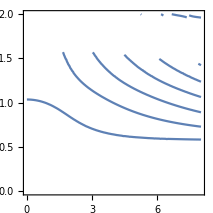

```mathematica
ContourPlot[{Disp2==0},{k, 0, 8}, {v, 0, 2},PerformanceGoal->"Quality"(*PlotPoints->200,MaxRecursion->2*)]
```

```mathematica
Clear[x]
```

```mathematica
DispF2[k_,ω_]= Re[((ks^2 - 2 kp^2) BesselJ[0, qp R] + 2 qp^2  (D[BesselJ[1, x], x]/. x-> qp R)) (ks^2 - 2 k^2/ R^2) BesselJ[1, qs R] + 4 k^2/ R^2 qp qs BesselJ[1, qp R]  (D[BesselJ[1, x], x]/. x-> qs R)];
Φ[y_]=y BesselJ[0,y]/BesselJ[1,y];
C0=Sqrt[E0/ρ];
a=(ω/k)^2(1+nu);
b=(1-2nu)(1-nu);
h1=k Sqrt[b a-1];
h2=k Sqrt[2 a-1];
DispF1[k_,ω_]=(a-1)^2 Φ[h1]-(b a-1)(a-Φ[h2]);
DispF3[k_,ω_]=(a-1)^2 h1 BesselJ[0,h1]BesselJ[1,h2]-(b a-1)(a  BesselJ[1,h1]BesselJ[1,h2]-h2  BesselJ[0,h2]BesselJ[1,h1]);
```

```mathematica
DispCurve1[k_]:=NSolve[DispF3[k,ω]==0&&0.5k<ω<1.05k,ω]⟦1,1,2⟧;
```

```mathematica
DispCurve1[k_]:=Re[FindRoot[DispF2[k,ω],{ω,0.5k,1.05k},Method->"Brent"]⟦1,2⟧];
```

```mathematica
DispCurve1[k_]:=NSolve[DispF1[k,ω]==0&&0.5k<ω<1.05k,ω]⟦1,1,2⟧;
```

```mathematica
DispF1[0.1,0.103]
```

-0.0456941+0. ⅈ

```mathematica
DispCurve1[k_]:=NSolve[DispF2[k,ω]==0&&0.5k<ω<1.05k,ω]⟦1,1,2⟧;
```

```mathematica
DispCurve1[0.1]
```

FindRoot::bbrac: Method -> Brent is only applicable to univariate real functions and requires two real starting values that bracket the root.

Re[ω]

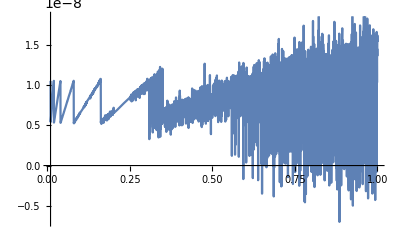

```mathematica
Plot[DispCurve1[k],{k, 0.01, 1}]
```

```mathematica
av=(v)^2(1+nu);
b=(1-2nu)(1-nu);
h1=k Sqrt[b av-1];
h2=k Sqrt[2 av-1];
DispFV1[k_,v_]=(av-1)^2 Φ[h1]-(b av-1)(av-Φ[h2]);
```

```mathematica
VelCurve1[k_]:=NSolve[DispFV1[k,v]==0&&0.5<v<1.05,v]⟦1,1,2⟧;
```

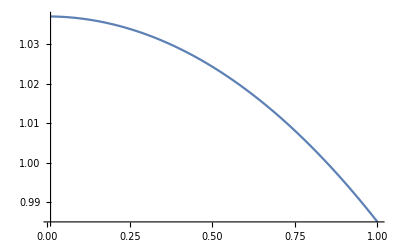

```mathematica
Plot[VelCurve1[k],{k, 0.01, 1}]
```